```mathematica
makeImage[pts_,expr_,pltRange1_,PltRange2_]:=Module[{},
Grid[
Graphics[{White, Thick, Line[#&/@pts]}, PlotRange -> {{-pltRange1,pltRange1},{-pltRange1,pltRange1}}, Axes -> True, Background -> GrayLevel[.6], ImageSize -> {500,500}, AxesLabel -> {Style["x",Italic], Style["y",Italic]},ImagePadding->20],

Graphics[{White, Thick, Line[{Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}& /@ #&/@pts]}, PlotRange -> {{-PltRange2,PltRange2},{-PltRange2,PltRange2}}, Axes -> True, Background -> RGBColor[.7, .5, .5], ImageSize -> {500,500}, AxesLabel -> {Style["u",Italic], Style["v",Italic]},ImagePadding->20]]]
```

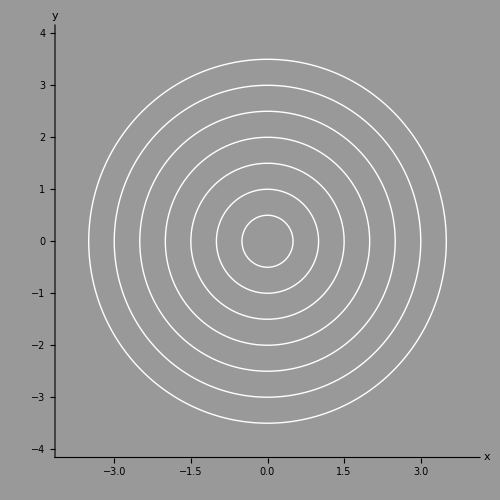
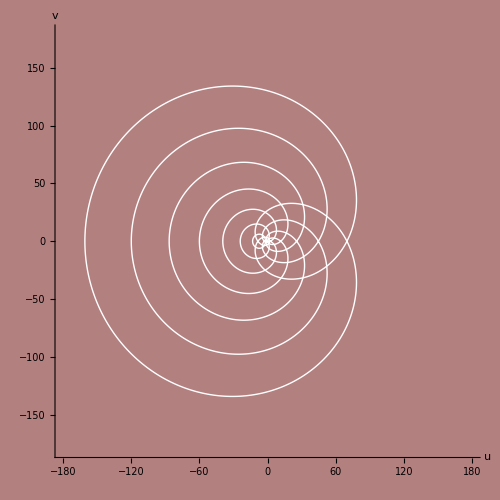
Grid[-Graphics-,-Graphics-]

```mathematica
ang=Range[0Pi,2Pi,.001];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[.5,3.5,.5]}];
pts=Transpose[#]&/@lists;
expr=(z-1)(z-2)(z-3);
n=4;
m=180;
makeImage[pts,expr,n,m]
```

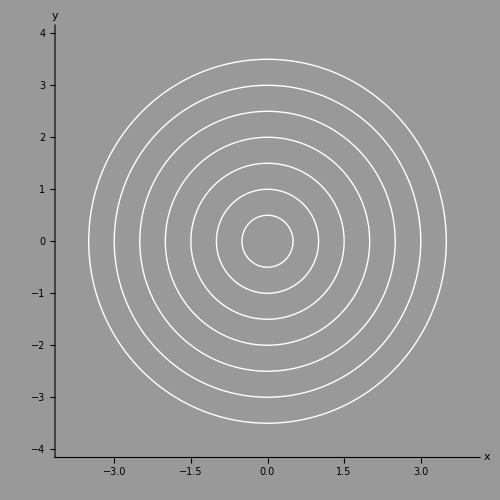
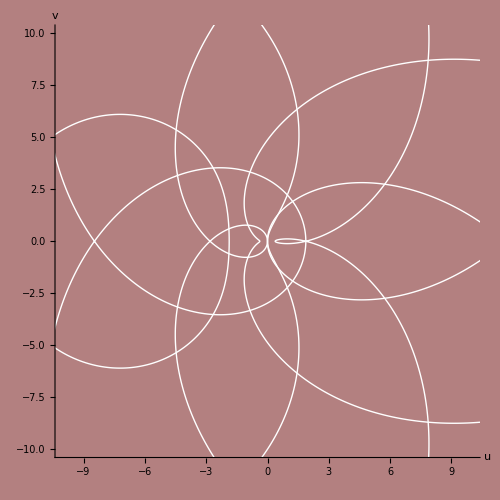
Grid[-Graphics-,-Graphics-]

```mathematica
expr=(z-1)(z-2)(z-3);
n=4;
m=10;
makeImage[pts,expr,n,m]
```

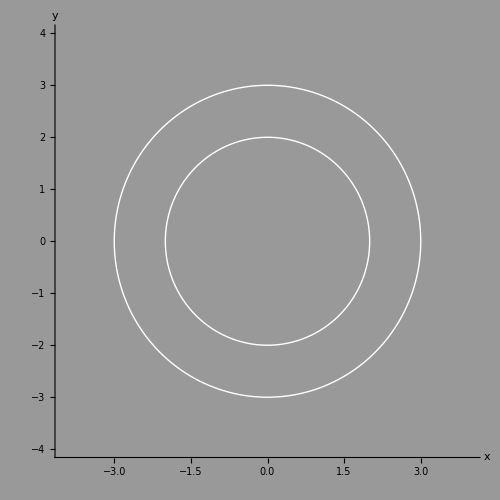
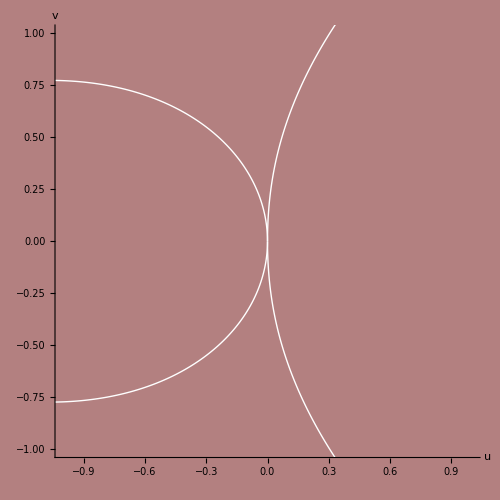
Grid[-Graphics-,-Graphics-]

```mathematica
ang=Range[.0Pi,2Pi,.001];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[2,3,1]}];
pts=Transpose[#]&/@lists;
expr=(z-1)(z-2)(z-3);
n=4;
m=1;
makeImage[pts,expr,n,m]
```